```mathematica
Needs["NDSolve`FEM`"]
m = ToElementMesh[
   DiscretizeGraphics[
    GraphicsComplex[{{0, 4}, {5, 4}, {5, 0}, {8, 0}, {8, 8}, {0, 8}}, 
     Polygon[{1, 2, 3, 4, 5, 6}]], MeshQualityGoal->1]];
```

```mathematica
getMidEleCoords = Compile[{{eleCoords, _Real, 2}},
   Mean[eleCoords], RuntimeAttributes -> {Listable}];

triToQuad = Compile[{{triInci, _Integer, 1}, {midInci, _Integer, 0}}, {
    {midInci, triInci[[6]], triInci[[1]], triInci[[4]]},
    {midInci, triInci[[4]], triInci[[2]], triInci[[5]]},
    {midInci, triInci[[5]], triInci[[3]], triInci[[6]]}
    }
   , RuntimeAttributes -> {Listable}
   ];

getConverterCode[TriangleElement] := triToQuad;
getNumOfResEle[TriangleElement] := 3
getConvertedEleType[TriangleElement] := QuadElement
```

```mathematica
coords = m["Coordinates"];
numOfCoords = Length[coords];
meshEle = m["MeshElements"];
inci = ElementIncidents[meshEle];
markers = ElementMarkers[meshEle];
eleCoords = GetElementCoordinates[coords, #] & /@ inci;
midEleCoords = getMidEleCoords[eleCoords];
numOfMidCoords = Length /@ midEleCoords;
temp = Join[{numOfCoords}, numOfMidCoords];
temp = FoldList[Plus, temp] + 1;
midEleInci = MapThread[Range, {Most[temp], Rest[temp - 1]}];
newCoords = Join[coords, Join @@ midEleCoords];
(*Max[midEleInci]===Length[newCoords]*)
```

```mathematica
newEle = Table[
   Block[{thisMeshEle, thisType, thisInci, thisMarker, converter, 
     newEle, newEleMarkers},
    thisMeshEle = meshEle[[i]];
    thisType = Head[thisMeshEle];
    thisInci = ElementIncidents[thisMeshEle];
    thisMarker = ElementMarkers[thisMeshEle];
    converter = getConverterCode[thisType];
    newEle = Join @@ converter[thisInci, midEleInci[[i]]];
    newEleMarkers = 
     Join @@ Transpose[
       ConstantArray[thisMarker, getNumOfResEle[thisType]]];
    getConvertedEleType[thisType][newEle, newEleMarkers]
    ]
   , {i, Length[meshEle]}];
```

```mathematica
mq1 = ToElementMesh["Coordinates" -> newCoords, 
  "MeshElements" -> newEle]
(* ElementMesh[{{0., 8.}, {0., 8.}}, {QuadElement["<" 1338 ">"]}] *)
```

ElementMesh[{{0.,8.},{0.,8.}},{QuadElement[<1389>]}]

```mathematica
m["Wireframe"]
```

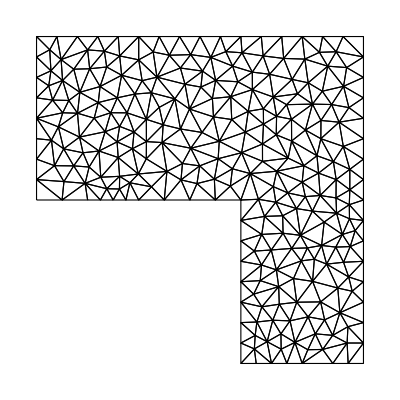

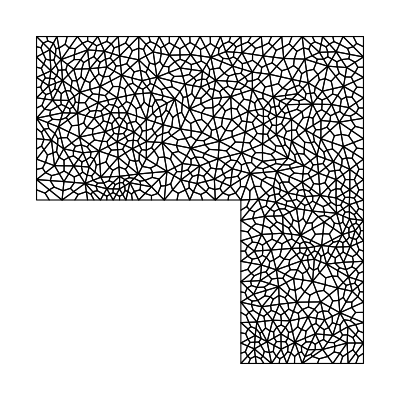

```mathematica
mq1["Wireframe"]
```

```mathematica
gtri = MeshConnectivityGraph[MeshRegion[m],0];
Adtri = Normal[AdjacencyMatrix[gtri]];
ArrayPlot[Adtri]
```

-Graphics-

```mathematica
g = MeshConnectivityGraph[MeshRegion[mq1],0];
Ad = Normal[AdjacencyMatrix[g]];
```

```mathematica
ArrayPlot[Ad]
```

-Graphics-

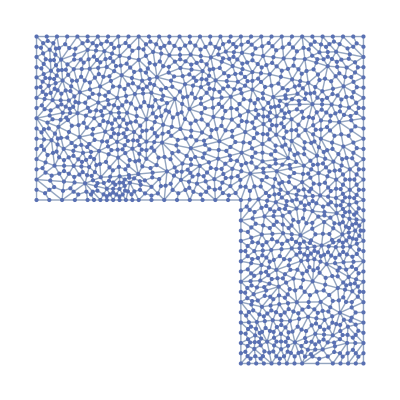

```mathematica
LaplacianSmoothing[AdjacencyMat_, VertexCoords_, Boundary_, Iterations_]:=(
VC = VertexCoords;
For[hh=0, hh<Iterations, hh++,
For[i=1, i<= Dimensions[AdjacencyMat][[1]], i++, Cave = {0,0}; ct = 0; If[Boundary[[i]]==0,For[j=1, j<=Dimensions[AdjacencyMat][[2]], j++, If[AdjacencyMat[[i,j]]==1,ct+=1;Cave +=VC[[j]]]];
Cave = Cave/ ct;  VC[[i]] = Cave]]];
Return[VC]
)
GraphPlot[g, VertexCoordinates->newCoords]
```

```mathematica
Wrap[i_,range_]:=Module[{iwrapped},
iwrapped = i;
 While[iwrapped<Min[Sequence@@range], iwrapped+=(Max[Sequence@@range]-Min[Sequence@@range] + 1)];
 While[iwrapped>Max[Sequence@@range], iwrapped-=(Max[Sequence@@range]-Min[Sequence@@range] + 1)];
iwrapped
]
```

```mathematica
IsOnPolygonBoundary[vertices_, x_, y_]:=Module[{LiesOn, i, vec, m, b},
LiesOn = False;
For[i=1, i<=Dimensions[vertices][[1]], i++, vec = vertices[[i]] - vertices[[Wrap[i+1, {1, Dimensions[vertices][[1]]}]]];If[vec[[1]] ==0, If[y< Max[vertices[[i,2]],vertices[ [Wrap[i+1, {1, Dimensions[vertices][[1]]}], 2]]]&& y> Min[vertices[[i,2]],vertices[ [Wrap[i+1, {1, Dimensions[vertices][[1]]}], 2]]] && x<vertices[[i,1]] + 0.001 && x>vertices[[i,1]] - 0.001, LiesOn = True;Break, Continue] , m = vec[[2]]/vec[[1]]; b = vertices[[i,2]]-vertices[[i,1]] * m  ; If[x*m +b <= y + 0.001 && x*m +b >= y - 0.001, LiesOn = True; Break, Continue]]];
LiesOn]
```

```mathematica
Bndry = Table[If[IsOnPolygonBoundary[{{0, 4}, {5, 4}, {5, 0}, {8, 0}, {8, 8}, {0, 8}}, Sequence @@ newCoords[[i]]], 1, 0], {i, 1, Dimensions[Ad][[1]]}];
```

```mathematica
CoordsSmoothening = {newCoords};
CoordsSmoothening//Dimensions
For[ih=1, ih< 20, ih++,CoordsSmoothening = Append[CoordsSmoothening, LaplacianSmoothing[Ad, CoordsSmoothening[[-1]], Bndry, 1]]];
```

{1,1455,2}

```mathematica
CoordsSmoothening//Dimensions
```

{20,1455,2}

```mathematica
Manipulate[GraphPlot[g, VertexCoordinates->CoordsSmoothening[[i]], Axes->False], {i,1, Dimensions[CoordsSmoothening][[1]],1}]
```

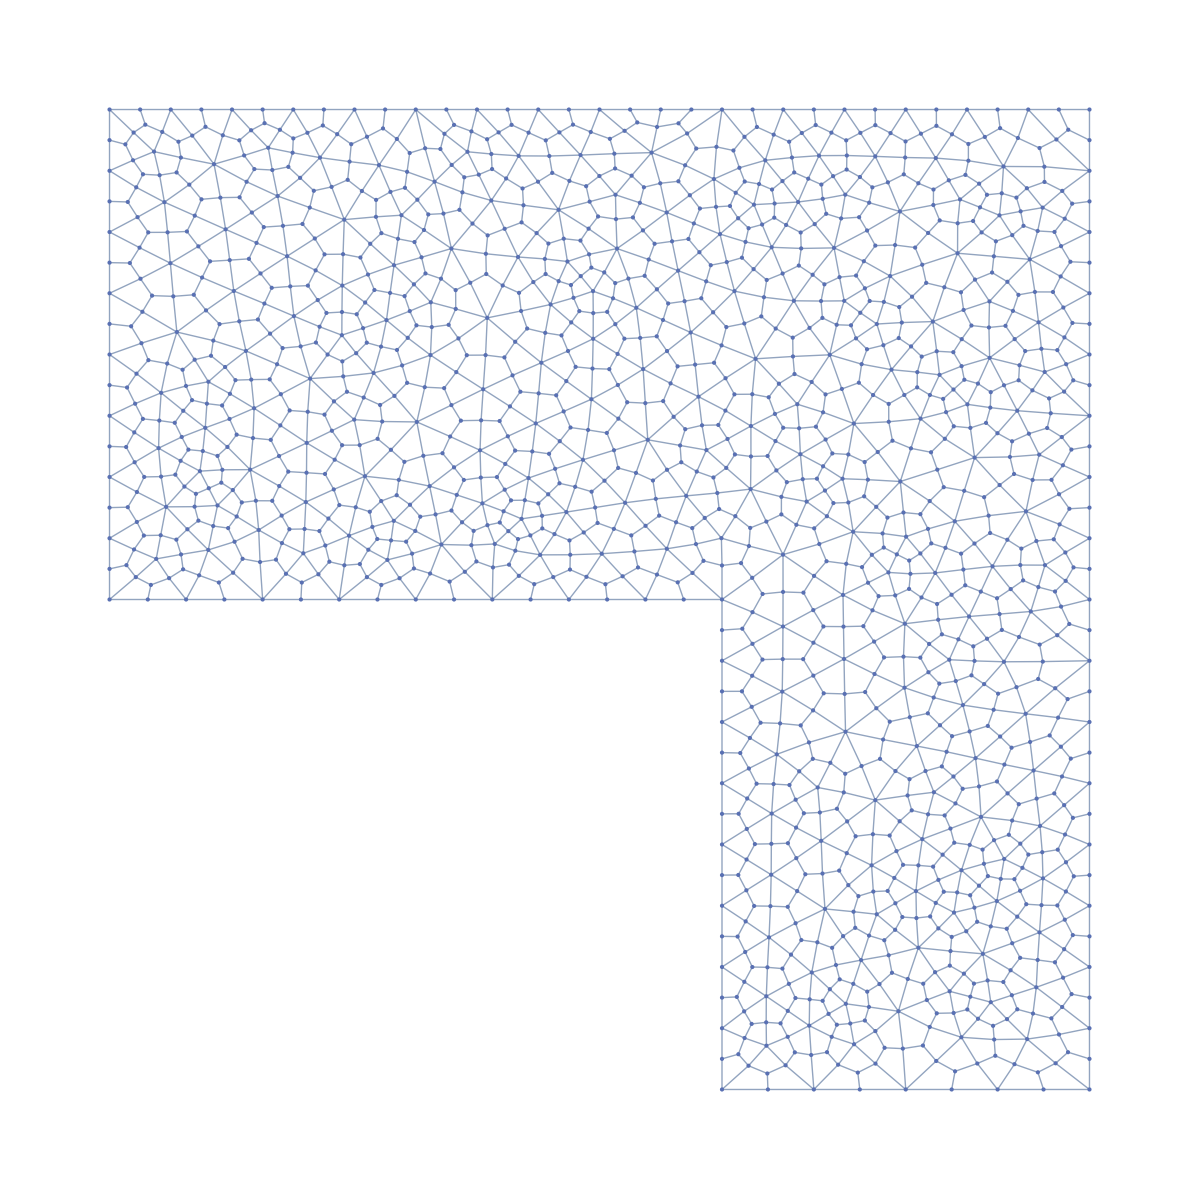

```mathematica
GraphPlot[g, VertexCoordinates->CoordsSmoother]
```

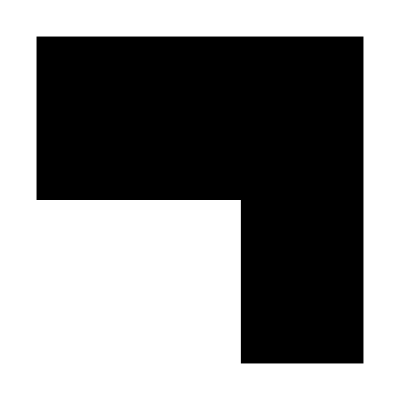

```mathematica
Graphics[GraphicsComplex[{{0, 4}, {5, 4}, {5, 0}, {8, 0}, {8, 8}, {0, 8}}, 
     Polygon[{1, 2, 3, 4, 5, 6}]]]
```

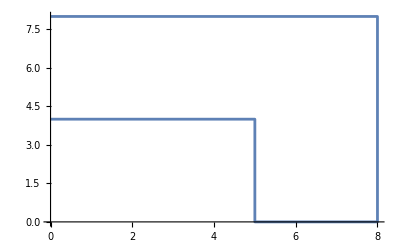

```mathematica
ListLinePlot[{{0, 4}, {5, 4}, {5, 0}, {8, 0}, {8, 8}, {0, 8}}]
```